## Assignment 1

4.1.1(b)

(1) Perform Gram-Schmidt orthogonalization by hand for the first three orthogonal polynomials extracted from the set {x^n}, n≥ 0, for the given inner products:

(b) (f,g) = ∫_(-∞)^∞ f^*g ⅇ^(-x^2)ⅆx (these will be proportional to Hermite polynomials).

### Solution

ψ_0=1;  ψ_1=x + a;  ∫_(-∞)^∞ ψ_1^*ψ_0 ⅇ^(-x^2)ⅆx=a √π so a=0.  ψ_2=x^2+ a x + b.

```mathematica
ψ0[x_]=1;
```

```mathematica
ψ1[x_]=x;
```

```mathematica
ψ2[x_] = x^2 + a x + b;
```

```mathematica
eq1=Integrate[ψ0[x] ψ2[x] Exp[-x^2],{x,-Infinity,Infinity}]==0
```

1/2 (1+2 b) √π==0

```mathematica
eq2=Integrate[ψ1[x] ψ2[x] Exp[-x^2],{x,-Infinity,Infinity}]==0
```

(a √π)/2==0

```mathematica
Solve[{eq1,eq2},{a,b}]
```

{{a→0,b→-1/2}}

```mathematica
ψ2[x_] = ψ2[x]/.%[[1]]
```

-1/2+x^2

4.1.5(d)

(5)  Find a generalized Fourier series representation for the following functions using the given orthogonal polynomials. Plot the resulting series for M=5, 10, and 15, along with the functions. In each case, evaluate Eq. (4.1.23) for the different M values to see whether convergence in the mean is being achieved.

(d) f(t) = t (1-t) /(2-t)  on -1≤ t≤ 1,  using Chebyshev polynomials of the first kind.

### Solution

The correct weight function for these Chebyshev polynomials:

```mathematica
p[t_]=(1-t^2)^(-1/2);
```

```mathematica
f[t_]=t(1-t)/(2-t);
```

```mathematica
?ChebyshevT
```

ChebyshevT[n,x] gives the Chebyshev polynomial of the first kind T_n(x).

```mathematica
Clear[c]
```

```mathematica
c[m_] :=c[m]= NIntegrate[p[t] f[t]ChebyshevT[m,t],{t,-1,1}]/NIntegrate[p[t] ChebyshevT[m,t]^2,{t,-1,1}]
```

```mathematica
fapp[x_,M_] := Sum[c[m] ChebyshevT[m,x],{m,0,M}]//Quiet
```

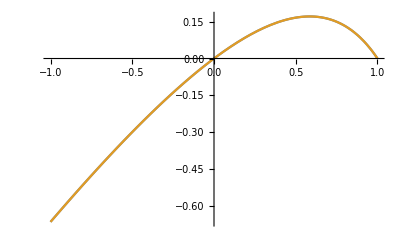

```mathematica
Plot[{f[x],fapp[x,10]}//Evaluate,{x,-1,1}]
```

```mathematica
error[M_]:= NIntegrate[p[t](f[t]-fapp[t,M])^2,{t,-1,1}]
```

```mathematica
Table[{M,error[M]},{M,5,15,5}]
```

{{5,1.23625×10^-6},{10,2.35847×10^-12},{15,4.49939×10^-18}}

Good convergence

4.1.8(e,f)

(8) Find an inner product for which the following operators are Hermitian with respect to functions that satisfy the given conditions:

(e) L̂=ⅆ^4/(ⅆ x^4)+ⅆ^2/(ⅆ x^2)+1 on [0,3], for functions that satisfy f=0 and f''=0 at the end points.

(f) L̂=ⅆ^2/(ⅆ x^2)+ h(x)ⅆ/ⅆx, on [-1,1] , for functions that satisfy f=0 at the end points,  and where h(x) is the Heaviside step function.

### Solution

#### (a)

One inner product is simply (f,g)=∫_0^3 ⅆx f^*g. L̂ is Hermitian wrt this inner product for functions that satisfy f=0 and f''=0 at the end points, which can be proven by 4 integrations by parts:
(f, L̂ g)=f^* (ⅆ^3 g)/(ⅆ x^3)|_0^3-∫_0^3 ⅆxⅆ/ⅆx f^*ⅆ^3/(ⅆ x^3)g+f^* ⅆg/ⅆx|_0^3-∫_0^3 ⅆxⅆ/ⅆx f^*ⅆ/ⅆx g+∫_0^3 ⅆx f^*g. The boundary terms vanish. Continuing, (f, L̂ g)=ⅆ/ⅆx f^*ⅆ^2/(ⅆ x^2)g|_0^3+∫_0^3 ⅆxⅆ^2/(ⅆ x^2)f^*ⅆ^2/(ⅆ x^2)g-g (ⅆ f^*)/ⅆx|_0^3+∫_0^3 ⅆx gⅆ^2/(ⅆ x^2)f^*+∫_0^3 ⅆx f^*g. Again, the boundary terms vanish. Only the first integral need now be integrated by parts, twice, and the result is (L̂ f, g) . QED.

#### (f)

We want to put  L̂=ⅆ^2/(ⅆ x^2)+ h(x)ⅆ/ⅆx in Sturm-Liouville form, L̂=1/(p(x))ⅆ/ⅆx r(x)ⅆ/ⅆx=(r(x))/(p(x))ⅆ^2/(ⅆ x^2)+1/(p(x))ⅆr/ⅆx ⅆ/ⅆx. 
Matching coefficients yields p(x)=r(x) and ⅆr/ⅆx=h(x) r(x). A solution of the second equation is r(x) = exp(u[x]) where u[x]=0 for x<0 and u[x]=x for x>0. Thus, the correct inner product is
			((f,g)=∫_-1^1 ⅆx exp(u[x])f^*g.

4.1.13(c)

(13) Find the eigenfunctions and eigenvalues for the following operators. If the operators are Hermitian with respect to some inner product, show directly that the eigenfunctions are orthogonal with respect to that inner product.

(c)  L̂ and boundary conditions given in Exercise (8)(f). (Hint: Match solutions for x<0 to those for x>0)

### Solution

For x<0 the eigenvalue equation is  ⅆ^2/(ⅆ x^2)ψ=-k^2 ψ, where -k^2 is the eigenvalue. A solution that matches the boundary condition at x=-1 is ψ=A sin k(x+1). For x>0 the eigenvalue equation is ⅆ^2/(ⅆ x^2)ψ+ⅆ/ⅆx ψ=-k^2ψ . The solution that matches the boundary condition at x=1 is ψ=B exp(-x/2)sin √(k^2-1/4)(x-1).
Match these solutions at x=0.

```mathematica
Clear["Global`*"]
```

```mathematica
ψ1[x_]= A Sin[k (x+1)];
ψ2[x_]= B Exp[-x/2] Sin[Sqrt[k^2-1/4](x-1)];
```

```mathematica
Solve[ψ1[0]==ψ2[0],A]
```

{{A→-B Csc[k] Sin[√(-1/4+k^2)]}}

```mathematica
ψ1'[0]-ψ2'[0]/.%[[1]]//Simplify
```

-1/2 B (√(-1+4 k^2) Cos[√(-1/4+k^2)]+(1+2 k Cot[k]) Sin[√(-1/4+k^2)])

```mathematica
eq[k_]=FullSimplify[% Sin[k]/B//Expand,k>0]
```

1/2 (-√(-1+4 k^2) Cos[√(-1/4+k^2)] Sin[k]-(2 k Cos[k]+Sin[k]) Sin[√(-1/4+k^2)])

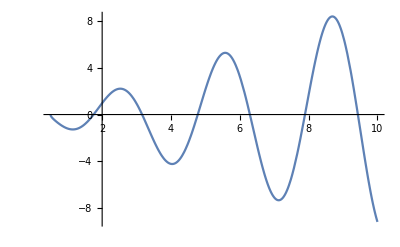

```mathematica
pl=Plot[eq[k],{k,1/2,10}]
```

```mathematica
kapprox[n_]= 1.6+n Pi/2;
```

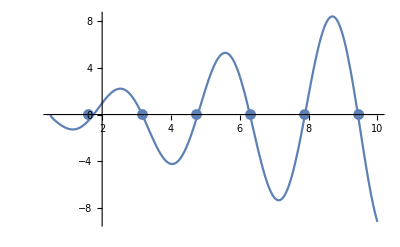

```mathematica
Table[{kapprox[n],0},{n,0,8}];
ListPlot[%];
Show[pl,%]
```

```mathematica
Clear[kn]
```

```mathematica
kn[n_]:=(kn[n]= k/.FindRoot[eq[k]==0,{k,kapprox[n]}])/; n∈ Integers
```

```mathematica
Table[kn[n],{n,0,10}]
```

{1.75107,3.16164,4.77788,6.29315,7.89359,9.43142,11.0239,12.5713,14.1592,15.7119,17.2968}

```mathematica
ψ[n_,x_]= Piecewise[{{ψ1[x]/.A-> -Csc[k] Sin[√(-1/4+k^2)],x≤ 0},{ψ2[x]/.B->1,x>0}}]/.k->kn[n]
```

Piecewise[{{-Csc[kn[n]] Sin[(1+x) kn[n]] Sin[√(-1/4+kn[n]^2)], x≤0}, {ⅇ^(-x/2) Sin[(-1+x) √(-1/4+kn[n]^2)], x>0}, {0, True}}]

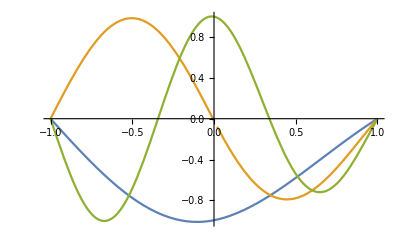

```mathematica
Plot[{ψ[0,x],ψ[1,x],ψ[2,x]},{x,-1,1}]
```

Show that the eiogenmodes are orthogonal numerically:

```mathematica
ip[f_,g_]:= NIntegrate[f g,{x,-1,0}]+NIntegrate[f g Exp[x],{x,0,1}]
```

```mathematica
Table[Table[ip[ψ[m,x],ψ[n,x]],{m,0,n}],{n,0,5}]//Chop
```

{{1.09386},{0,0.984512},{0,0,1.01236},{0,0,0,0.996064},{0,0,0,0,1.00452},{0,0,0,0,0,0.998245}}

Analytically:

```mathematica
ipa[f_,g_]:= Integrate[f g,{x,-1,0}]+Integrate[f g Exp[x],{x,0,1}]
```

```mathematica
ipa[ψ[m,x],ψ[n,x]]
```

-((Cot[kn[m]] kn[m]-Cot[kn[n]] kn[n]) Sin[√(-1/4+kn[m]^2)] Sin[√(-1/4+kn[n]^2)])/(kn[m]^2-kn[n]^2)+1/(2 (kn[m]^2-kn[n]^2))(Cos[1/2 √(-1+4 kn[n]^2)] √(-1+4 kn[n]^2) Sin[1/2 √(-1+4 kn[m]^2)]-Cos[1/2 √(-1+4 kn[m]^2)] √(-1+4 kn[m]^2) Sin[1/2 √(-1+4 kn[n]^2)])

Moanipulate this using the dispersion relation for k:

```mathematica
FullSimplify[%,eq[kn[n]]==0&&eq[kn[m]]==0]
```

1/(2 (kn[m]^2-kn[n]^2))(Cos[1/2 √(-1+4 kn[n]^2)] √(-1+4 kn[n]^2) Sin[1/2 √(-1+4 kn[m]^2)]+2 (-Cot[kn[m]] kn[m]+Cot[kn[n]] kn[n]) Sin[√(-1/4+kn[m]^2)] Sin[√(-1/4+kn[n]^2)]-Cos[1/2 √(-1+4 kn[m]^2)] √(-1+4 kn[m]^2) Sin[1/2 √(-1+4 kn[n]^2)])

```mathematica
Solve[eq[k]==0, Cos[√(-1/4+k^2)]]
```

{{Cos[√(-1/4+k^2)]→-((1+2 k Cot[k]) Sin[√(-1/4+k^2)])/(√(-1+4 k^2))}}

```mathematica
%%/.Cos[1/2 √(-1+4 k_^2)]->-((1+2 k Cot[k]) Sin[√(-1/4+k^2)])/(√(-1+4 k^2))
```

1/(2 (kn[m]^2-kn[n]^2))(2 (-Cot[kn[m]] kn[m]+Cot[kn[n]] kn[n]) Sin[√(-1/4+kn[m]^2)] Sin[√(-1/4+kn[n]^2)]-(1+2 Cot[kn[n]] kn[n]) Sin[1/2 √(-1+4 kn[m]^2)] Sin[√(-1/4+kn[n]^2)]+(1+2 Cot[kn[m]] kn[m]) Sin[√(-1/4+kn[m]^2)] Sin[1/2 √(-1+4 kn[n]^2)])

```mathematica
FullSimplify[%]
```

0

4.2.2

(2) When one cooks using radiant heat (under a broiler, for example), there is a heat flux Γ_r due to the radiation, incident on the surface of the food. On the other hand, the food is typically suspended (on a grill or spit for example)  in such a way that it cannot conduct heat very well to the environment, so that little heat is reradiated.  Under these conditions, find the time required to raise the internal temperature of a slab of meat  of thickness L=5 cm from T=20 °C to T=90 °C. Animate the solution for T(x,t) up to this time. Take χ= 3×10^-7 m^2/s, C=3×10^6 J/(m^3 K), and assume that both faces of the meat are subjected to the same flux of heat, equal to 10 kW/m^2(a typical value in an oven).
(Note: there is NO equilibrium solution for this problem, so separation of variables will not work. Instead, put the PDE in standard form.)

### Solution

First write T(x,t) = u(x,t) + ΔT(x,t) where u(x,t)  satisfies the inhomogeous boundary conditions, -κ ∂_x u(0,t) =Γ_r=10,000 W/m^2, -κ ∂_x u(L,t) = -Γ_r. 

Choose linear variation in the slope:
∂_x u(x,t) =-Γ_r/κ  (1 - 2x/L). This implies

```mathematica
Clear["Global`*"]
```

```mathematica
u[x_,t_] = -Γ/κ (x - x^2/L);
```

So ΔT satisfies the heat equation with a source, (∂ΔT)/(∂t)=χ (∂^2 ΔT)/(∂x^2)+ S(x,t)  where

```mathematica
S[x_,t_] = χ D[u[x,t],{x,2}] - D[u[x,t],t]
```

(2 Γ χ)/(L κ)

The source is actually constant in space and time. The boundary conditions on ΔT are Neumann, because we specified the flux at the boundaries: ∂_x ΔT(0,t) = ∂_x ΔT(L,t)=0. We now solve for ΔT(x,t) via a Fourier series of the Neuman eigenmodes, which satisfy
	χ(∂^2 ψ)/(∂x^2)=λ ψ(x), ∂_x ψ(0) = ∂_x ψ(L)=0 .
The eigenmodes are

```mathematica
ψ[n_,x_] = Cos[n Pi x/L];
λ[n_] = -χ (n Pi/L)^2;
```

for n=0,1,2,....

If we now write ΔT(x,t) = ∑_(n=0)^∞ c_n(t) ψ_n(x), the usual argument implies that c_n(t) satisfies the equation
(ċ)_n=λ_n c_n + s_n, where s_n(t) = (ψ_n, S)/(ψ_n, ψ_n). But in this case, only s_0  is nonzero, and it is constant:

```mathematica
s[0] = S[x,t]
```

(2 Γ χ)/(L κ)

Since λ[0]=0,

```mathematica
c[0,t_] =t s[0] + A[0];
```

and for n>0

```mathematica
c[n_,t_] = A[n] Exp[λ[n] t] ;
```

Finally, we require the A[n]'s; they are found from the equation c_n(0) = (ψ_n(x),T_i(x) - u(x,0))/(ψ_n,ψ_n)

```mathematica
Ti[x_] = 20;
```

```mathematica
Solve[c[0,0] == Integrate[ψ[0,x] (Ti[x] - u[x,0]),{x,0,L}]/Integrate[ψ[0,x]^2,{x,0,L}],A[0]]
```

{{A[0]→(L Γ+120 κ)/(6 κ)}}

```mathematica
c[0,t_] = c[0,t] /.%[[1]]
```

(L Γ+120 κ)/(6 κ)+(2 t Γ χ)/(L κ)

```mathematica
Solve[c[n,0] == Simplify[Integrate[ψ[n,x] (Ti[x] - u[x,0]),{x,0,L}]/Integrate[ψ[n,x]^2,{x,0,L}],n∈Integers],A[n]]
```

{{A[n]→-(2 (1+(-1)^n) L Γ)/(n^2 π^2 κ)}}

```mathematica
c[n_,t_] = c[n,t] /.%[[1]]
```

-(2 (1+(-1)^n) ⅇ^(-(n^2 π^2 t χ)/L^2) L Γ)/(n^2 π^2 κ)

```mathematica
χ = 3.*^-7; CC= 3*^6;
κ = χ CC;
L = 0.05;
Γ = 10000;
```

```mathematica
ΔT[x_,t_] = Sum[c[n,t] ψ[n,x],{n,0,20}];
```

```mathematica
T[x_,t_] = u[x,t] + ΔT[x,t];
```

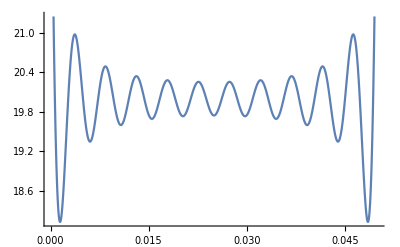

```mathematica
Plot[T[x,0],{x,0,L}]
```

Gibb's phenomenon, but that’s OK.

Temperature in the cneter of the slab versus time:

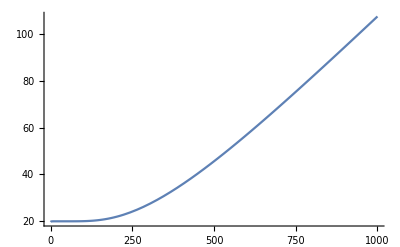

```mathematica
Plot[T[L/2,t],{t,0,1000}]
```

When does the central temperature reach 90C?

```mathematica
FindRoot[T[L/2,t]==90,{t,700,800}]
```

{t→865.218}

So the meat takes 865 seconds to cook.

```mathematica
Table[Plot[T[x,t],{x,0,L},PlotRange->{0,250},PlotLabel->"T[x,"<>ToString[t]<>" ]",AxesLabel->{"x",""}],{t,20,860,20}];
```

```mathematica
ListAnimate[%]
```

Note that at late times, the only term left in the sum is the n=0 term because the other terms decay away with time, implying that T(x,t) = u(x) + A(0) + t s(0), a quadratic function of x increasing linearly with time.